```mathematica
imp=Import["C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\Praca wyjścia\\rich.txt","Table"]
RichData=imp[[2;;Length[imp]]]
Needs["ErrorBarPlots`"]
```

{{Iz,Ia,Tup,Tdown},{1199,1.3,1020,1040},{1249,2.7,1040,1060},{1299,5.3,1060,1060},{1350,10.5,1100,1100},{1403,20.4,1100,1120},{1452,37.,1120,1120},{1503,66.6,1140,1140},{1549,108.8,1160,1160},{1600,187.6,1180,1180},{1649,300,1200,1220}}

{{1199,1.3,1020,1040},{1249,2.7,1040,1060},{1299,5.3,1060,1060},{1350,10.5,1100,1100},{1403,20.4,1100,1120},{1452,37.,1120,1120},{1503,66.6,1140,1140},{1549,108.8,1160,1160},{1600,187.6,1180,1180},{1649,300,1200,1220}}

```mathematica
IData=RichData[[All,1;;2]]
```

{{1199,1.3},{1249,2.7},{1299,5.3},{1350,10.5},{1403,20.4},{1452,37.},{1503,66.6},{1549,108.8},{1600,187.6},{1649,300}}

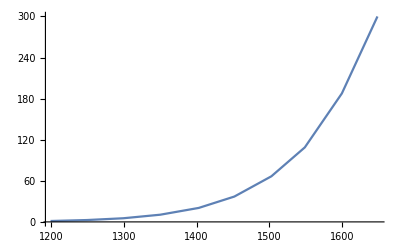

```mathematica
ListLinePlot[IData]
```

```mathematica
TData=RichData[[All,{1,3,4}]]
TempData={{#[[1]],(#[[2]]+#[[3]])/2+273},ErrorBar[0.003#[[1]]+1,20]}&/@TData
```

{{1199,1020,1040},{1249,1040,1060},{1299,1060,1060},{1350,1100,1100},{1403,1100,1120},{1452,1120,1120},{1503,1140,1140},{1549,1160,1160},{1600,1180,1180},{1649,1200,1220}}

{{{1199,1303},ErrorBar[4.597,20]},{{1249,1323},ErrorBar[4.747,20]},{{1299,1333},ErrorBar[4.897,20]},{{1350,1373},ErrorBar[5.05,20]},{{1403,1383},ErrorBar[5.209,20]},{{1452,1393},ErrorBar[5.356,20]},{{1503,1413},ErrorBar[5.509,20]},{{1549,1433},ErrorBar[5.647,20]},{{1600,1453},ErrorBar[5.8,20]},{{1649,1483},ErrorBar[5.947,20]}}

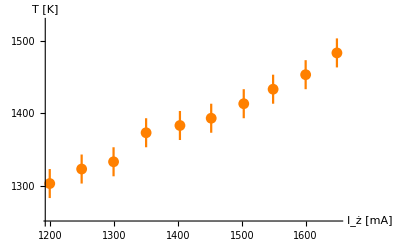

```mathematica
ErrorListPlot[TempData,AxesLabel->{"I_(:017c) [mA]","T [K]"},PlotStyle->{Orange},Ticks->{Automatic,Range[1100,1600,25]},PlotRange->{1250,1525},PlotStyle->{PointSize[Tiny]}]
```

1.38066×10^-23

1/10000

6.24151×10^18

{{8.90594,-2.56956},{8.77131,-1.86914},{8.70551,-1.20974},{8.45189,-0.585206},{8.39078,0.0644397},{8.33054,0.645413},{8.21263,1.20469},{8.09801,1.66739},{7.98654,2.18447},{7.82498,Log[30000000/2199289]}}

{{{8.90594,-2.56956},ErrorBar[0.136699,0.192237]},{{8.77131,-1.86914},ErrorBar[0.132597,0.108012]},{{8.70551,-1.20974},ErrorBar[0.130615,0.0696301]},{{8.45189,-0.585206},ErrorBar[0.123116,0.0491333]},{{8.39078,0.0644397},ErrorBar[0.121342,0.0392167]},{{8.33054,0.645413},ErrorBar[0.119606,0.0343907]},{{8.21263,1.20469},ErrorBar[0.116244,0.0314617]},{{8.09801,1.66739},ErrorBar[0.113022,0.0298436]},{{7.98654,2.18447},ErrorBar[0.109932,0.0286487]},{{7.82498,Log[30000000/2199289]},ErrorBar[0.105529,0.0276724]}}

FittedModel[41.6304-4.94942 x]

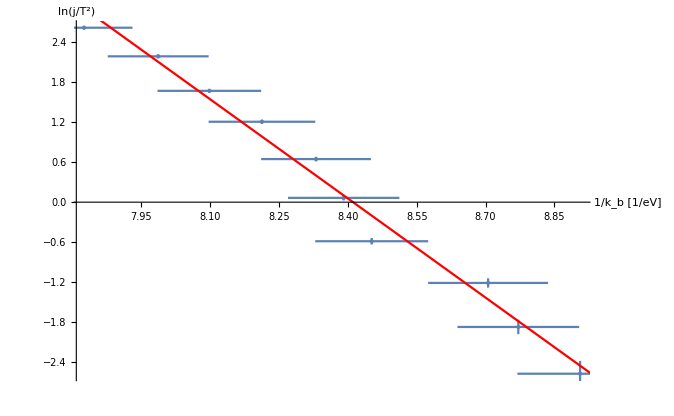

4.94942

| Estimate | Standard Error | t-Statistic | P-Value
1 | 41.6304 | 1.87349 | 22.2208 | 1.77832×10^-8
x | -4.94942 | 0.223715 | -22.1238 | 1.84073×10^-8

```mathematica
k=1.380658 10^-23
d=10^-4
norm=6.24150913×10^18
a=7.7;
b=9;
RichMetData={1/(k  ((#[[3]]+#[[4]])/2+273)norm) ,Log[(#[[2]] 10^-3)/(d^2((#[[3]]+#[[4]])/2+273)^2)]}&/@RichData
ErrorRichMetData={{1/(k  ((#[[3]]+#[[4]])/2+273)norm) ,Log[(#[[2]] 10^-3)/(d^2((#[[3]]+#[[4]])/2+273)^2)]},ErrorBar[20/(k ((#[[3]]+#[[4]])/2+273)^2 norm),(0.00021/(#[[2]] 10^-3)+40/((#[[3]]+#[[4]])/2+273))]}&/@RichData
RichMetFit=LinearModelFit[RichMetData,x,x]
Show[ErrorListPlot[ErrorRichMetData,PlotStyle->{PointSize[Tiny]}],Plot[Normal[RichMetFit],{x,a,b},PlotStyle->Red],AxesLabel->{"1/k_b [1/eV]","ln(j/T^2)"}]
Normal[RichMetFit][[2]][[1]]*(-1)
RichMetFit["ParameterTable"]
```

```mathematica
impd=Import["C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\Praca wyjścia\\dav.txt","Table"]
DaviData=impd[[2;;Length[impd]]]
```

{{Iz,R,Ia,dIz},{24.98,11,5.358,2.339},{23.97,10.6,5.142,2.258},{23.01,10.3,4.819,2.099},{21.96,9.9,4.431,1.945},{20.97,9.5,4.006,1.754},{19.87,9.1,3.503,1.525},{19.02,8.6,2.958,1.226},{18.06,8.34,2.348,0.991},{17.05,7.91,1.703,0.68},{16.01,7.46,1.035,0.515},{14.99,7.02,0.497,0.263},{13.96,6.43,0.144,0.394},{13.02,6.05,-,-},{12.06,5.55,-,-},{11.04,5.04,-,-},{10.02,4.55,-,-},{9.01,4.12,-,-},{7.99,3.8,-,-},{7.03,3.55,-,-},{6.09,3.37,-,-},{5.03,3.21,-,-},{4.01,3.1,-,-},{2.94,3.01,-,-},{2.02,3.01,-,-},{1.05,3.01,-,-}}

{{24.98,11,5.358,2.339},{23.97,10.6,5.142,2.258},{23.01,10.3,4.819,2.099},{21.96,9.9,4.431,1.945},{20.97,9.5,4.006,1.754},{19.87,9.1,3.503,1.525},{19.02,8.6,2.958,1.226},{18.06,8.34,2.348,0.991},{17.05,7.91,1.703,0.68},{16.01,7.46,1.035,0.515},{14.99,7.02,0.497,0.263},{13.96,6.43,0.144,0.394},{13.02,6.05,-,-},{12.06,5.55,-,-},{11.04,5.04,-,-},{10.02,4.55,-,-},{9.01,4.12,-,-},{7.99,3.8,-,-},{7.03,3.55,-,-},{6.09,3.37,-,-},{5.03,3.21,-,-},{4.01,3.1,-,-},{2.94,3.01,-,-},{2.02,3.01,-,-},{1.05,3.01,-,-}}

```mathematica
RData=DaviData[[All,{1,2}]]
RData={#[[1]],#[[2]]10}&/@RData
```

{{24.98,11},{23.97,10.6},{23.01,10.3},{21.96,9.9},{20.97,9.5},{19.87,9.1},{19.02,8.6},{18.06,8.34},{17.05,7.91},{16.01,7.46},{14.99,7.02},{13.96,6.43},{13.02,6.05},{12.06,5.55},{11.04,5.04},{10.02,4.55},{9.01,4.12},{7.99,3.8},{7.03,3.55},{6.09,3.37},{5.03,3.21},{4.01,3.1},{2.94,3.01},{2.02,3.01},{1.05,3.01}}

{{24.98,110},{23.97,106.},{23.01,103.},{21.96,99.},{20.97,95.},{19.87,91.},{19.02,86.},{18.06,83.4},{17.05,79.1},{16.01,74.6},{14.99,70.2},{13.96,64.3},{13.02,60.5},{12.06,55.5},{11.04,50.4},{10.02,45.5},{9.01,41.2},{7.99,38.},{7.03,35.5},{6.09,33.7},{5.03,32.1},{4.01,31.},{2.94,30.1},{2.02,30.1},{1.05,30.1}}

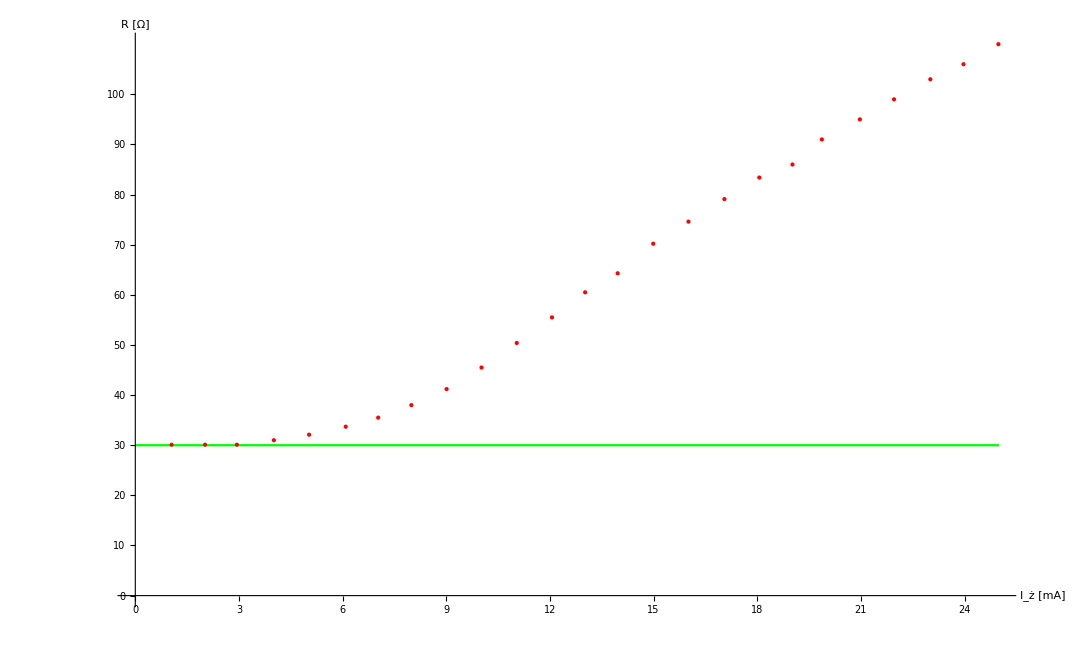

```mathematica
Show[ListPlot[RData,AxesLabel->{"I_(:017c) [mA]","R [Ω]"},PlotStyle->{Red,PointSize[Medium]},Ticks->{Automatic,Range[0,100,10]}],Plot[30,{x,0,25},PlotStyle->Green]]
```

```mathematica
alpha=4.5 10^-3
R0=30
Tem=(#[[2]]10/R0-1)/alpha&/@DaviData
```

0.0045

30

{592.593,562.963,540.741,511.111,481.481,451.852,414.815,395.556,363.704,330.37,297.778,254.074,225.926,188.889,151.111,114.815,82.963,59.2593,40.7407,27.4074,15.5556,7.40741,0.740741,0.740741,0.740741}

```mathematica
RRT=Transpose[{DaviData[[All,2]],Tem}]
RRT={#[[2]],#[[1]]10/R0}&/@RRT
```

{{11,592.593},{10.6,562.963},{10.3,540.741},{9.9,511.111},{9.5,481.481},{9.1,451.852},{8.6,414.815},{8.34,395.556},{7.91,363.704},{7.46,330.37},{7.02,297.778},{6.43,254.074},{6.05,225.926},{5.55,188.889},{5.04,151.111},{4.55,114.815},{4.12,82.963},{3.8,59.2593},{3.55,40.7407},{3.37,27.4074},{3.21,15.5556},{3.1,7.40741},{3.01,0.740741},{3.01,0.740741},{3.01,0.740741}}

{{592.593,11/3},{562.963,3.53333},{540.741,3.43333},{511.111,3.3},{481.481,3.16667},{451.852,3.03333},{414.815,2.86667},{395.556,2.78},{363.704,2.63667},{330.37,2.48667},{297.778,2.34},{254.074,2.14333},{225.926,2.01667},{188.889,1.85},{151.111,1.68},{114.815,1.51667},{82.963,1.37333},{59.2593,1.26667},{40.7407,1.18333},{27.4074,1.12333},{15.5556,1.07},{7.40741,1.03333},{0.740741,1.00333},{0.740741,1.00333},{0.740741,1.00333}}

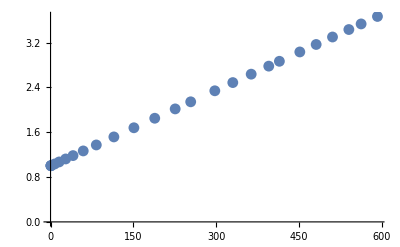

```mathematica
ListPlot[RRT]
```

```mathematica
e=1
kb=8.617 10^-5
FullData=Transpose[{DaviData,Tem}]
FullData=Flatten[#]&/@FullData
T0=293.15
T[R_]:=(R/R0-Normal[TempFit][[1]])/(Normal[TempFit][[2]][[1]])
AdA={(2e#[[1]]#[[2]] 10^-2#[[4]])/(#[[3]])-2kb (T[#[[2]]]-T0)}&/@FullData
```

1

0.00008617

{{{24.98,11,5.358,2.339},592.593},{{23.97,10.6,5.142,2.258},562.963},{{23.01,10.3,4.819,2.099},540.741},{{21.96,9.9,4.431,1.945},511.111},{{20.97,9.5,4.006,1.754},481.481},{{19.87,9.1,3.503,1.525},451.852},{{19.02,8.6,2.958,1.226},414.815},{{18.06,8.34,2.348,0.991},395.556},{{17.05,7.91,1.703,0.68},363.704},{{16.01,7.46,1.035,0.515},330.37},{{14.99,7.02,0.497,0.263},297.778},{{13.96,6.43,0.144,0.394},254.074},{{13.02,6.05,-,-},225.926},{{12.06,5.55,-,-},188.889},{{11.04,5.04,-,-},151.111},{{10.02,4.55,-,-},114.815},{{9.01,4.12,-,-},82.963},{{7.99,3.8,-,-},59.2593},{{7.03,3.55,-,-},40.7407},{{6.09,3.37,-,-},27.4074},{{5.03,3.21,-,-},15.5556},{{4.01,3.1,-,-},7.40741},{{2.94,3.01,-,-},0.740741},{{2.02,3.01,-,-},0.740741},{{1.05,3.01,-,-},0.740741}}

{{24.98,11,5.358,2.339,592.593},{23.97,10.6,5.142,2.258,562.963},{23.01,10.3,4.819,2.099,540.741},{21.96,9.9,4.431,1.945,511.111},{20.97,9.5,4.006,1.754,481.481},{19.87,9.1,3.503,1.525,451.852},{19.02,8.6,2.958,1.226,414.815},{18.06,8.34,2.348,0.991,395.556},{17.05,7.91,1.703,0.68,363.704},{16.01,7.46,1.035,0.515,330.37},{14.99,7.02,0.497,0.263,297.778},{13.96,6.43,0.144,0.394,254.074},{13.02,6.05,-,-,225.926},{12.06,5.55,-,-,188.889},{11.04,5.04,-,-,151.111},{10.02,4.55,-,-,114.815},{9.01,4.12,-,-,82.963},{7.99,3.8,-,-,59.2593},{7.03,3.55,-,-,40.7407},{6.09,3.37,-,-,27.4074},{5.03,3.21,-,-,15.5556},{4.01,3.1,-,-,7.40741},{2.94,3.01,-,-,0.740741},{2.02,3.01,-,-,0.740741},{1.05,3.01,-,-,0.740741}}

293.15

{{2.41478},{2.24763},{2.08107},{1.92549},{1.76181},{1.59208},{1.37419},{1.28997},{1.09604},{1.20807},{1.13367},{4.93262},{1.59642},{1.3602},{1.13492},{0.934428},{0.765492},{0.63065},{0.522808},{0.434336},{0.346968},{0.272779},{0.201244},{0.14586},{0.0874655}}

```mathematica
Length[AdA]
Length[FullData]
```

25

25

```mathematica
DaviData//TableForm
```

24.98 | 11 | 5.358 | 2.339
23.97 | 10.6 | 5.142 | 2.258
23.01 | 10.3 | 4.819 | 2.099
21.96 | 9.9 | 4.431 | 1.945
20.97 | 9.5 | 4.006 | 1.754
19.87 | 9.1 | 3.503 | 1.525
19.02 | 8.6 | 2.958 | 1.226
18.06 | 8.34 | 2.348 | 0.991
17.05 | 7.91 | 1.703 | 0.68
16.01 | 7.46 | 1.035 | 0.515
14.99 | 7.02 | 0.497 | 0.263
13.96 | 6.43 | 0.144 | 0.394
13.02 | 6.05 | - | -
12.06 | 5.55 | - | -
11.04 | 5.04 | - | -
10.02 | 4.55 | - | -
9.01 | 4.12 | - | -
7.99 | 3.8 | - | -
7.03 | 3.55 | - | -
6.09 | 3.37 | - | -
5.03 | 3.21 | - | -
4.01 | 3.1 | - | -
2.94 | 3.01 | - | -
2.02 | 3.01 | - | -
1.05 | 3.01 | - | -

```mathematica
WorthA=Transpose[AdA[[1;;11]]][[1]]
```

{2.41478,2.24763,2.08107,1.92549,1.76181,1.59208,1.37419,1.28997,1.09604,1.20807,1.13367}

```mathematica
TempData=Import["C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\Praca wyjścia\\T.txt","Table"]
```

{{273,0.911},{293,1},{300,1.03},{400,1.467},{500,1.924},{600,2.41},{700,2.93},{800,3.46},{900,4},{1000,4.54},{1100,5.08},{1200,5.65},{1300,6.22},{1400,6.78},{1500,7.36},{1600,7.93},{1700,8.52},{1800,9.12}}

```mathematica
TempFit=LinearModelFit[TempData,x,x]
```

FittedModel[-0.71812+0.00537016 x]

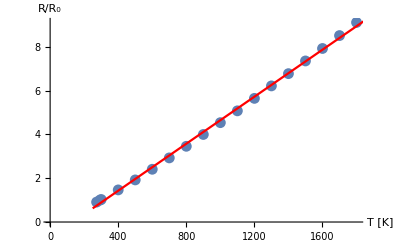

```mathematica
Show[ListPlot[TempData],Plot[Normal[TempFit],{x,250,1850},PlotStyle->Red],AxesLabel->{"T [K]","R/R_0"}]
```

```mathematica
Mean[WorthA]
```

1.64771

```mathematica
StandardDeviation[WorthA]
```

0.468405